# CMOS circuit analysis

```mathematica
SetDirectory["D:\\Math\MathmaticaCal\nb"];
```

SetDirectory::cdir: 不能把当前目录设为 D:\Math\MathmaticaCal
b.

### NMOS model

#### physical parameters

```mathematica
nm=10^-9;(*nanometer*)
um=10^-6;(*micrometer*)
NVTO=0.7;(*threshold voltage when VSB is 0, unit: V*)
NGAMMA=0.45;(*substrate bias effect coefficient, unit: V^(1/2)*)
NPHI=0.9;(*potential difference, unit: V*)
TOX=9 nm;(*oxide thickness, unit: m*)
NSUB=9 10^14;(*substrate impurity concentration, unit: cm^-3*)
NUO=350 10^-4;(*channel mobility, unit: m^2/Vs*)
NLAMBDA=0.1;(*channel length modulation coefficient, unit: V^-1*)
```

#### device parameters

```mathematica
COX=3.9 10^-3;(*capacitance, unit: F/m^2*)
```

#### current charateristics

triode region

```mathematica
Subscript[ⅈ, DS]=β (Subscript[V, DS] Subscript[V, EFF]-(Subscript[V, DS] Subscript[V, DS])/2);
```

```mathematica
NIDT[VG_,VD_,VS_,W_,L_,VB_]:=NBETA (NVEFF (VD-VS)-((VD-VS) (VD-VS))/2)/.NBETA->(COX NUO W)/L/.NVEFF->VG-VS-NVTH/.NVTH->NGAMMA (√Abs[NPHI+VS-VB]-√NPHI)+NVTO
```

saturation region

```mathematica
Subscript[ⅈ, DS]=1/2 β Subscript[ⅈ, DS] or Subscript[V, EFF]^2=1/2 β Subscript[V, EFF]^2 (λ Subscript[V, DS]+1);
```

Set::write: 1/2 or β V_EFF^2 (β (-V_DS^2/2+V_DS V_EFF)) 中的标签 Times 被保护.

```mathematica
NIDS[VG_,VD_,VS_,W_,L_,VB_]:=0.5 NBETA (NVEFF*NVEFF) (*(1+LAMBDA (VD-VS))*)/.NBETA->NUO COX W/L/.NVEFF->VG-VS-NVTH/.NVTH->NVTO+NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])
```

```mathematica
NIds[VG_,VD_,VS_,W_,L_,VB_]:=NIDT[VG,VD,VS,W,L,VB]/;VG-NVTO-NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])≥VD
NIds[VG_,VD_,VS_,W_,L_,VB_]:=NIDS[VG,VD,VS,W,L,VB]/;VG-NVTO-NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])<VD
(*NIds[VGS_,VDS_,W_,L_,VSB_]:=0/;VGS-NVTO-NGAMMA (Sqrt[Abs[NPHI+VSB]]-Sqrt[NPHI])<0*)
```

small signal model

```mathematica
Nη[VS_,VB_]:=NGAMMA/(2 Sqrt[NPHI+VS-VB])
Nr0[VG_,VD_,VS_,W_,L_,VB_]:=1/(NLAMBDA NIDS[VG,VD,VS,W,L,VB])
```

### PMOS model

#### physical parameters

```mathematica
nm=10^-9;(*nanometer*)
um=10^-6;(*micrometer*)
PVTO=-0.8;(*threshold voltage when VSB is 0, unit: V*)
PGAMMA=0.4;(*substrate bias effect coefficient, unit: V^(1/2)*)
PPHI=0.8;(*potential difference, unit: V*)
TOX=9 nm;(*oxide thickness, unit: m*)
PSUB=5 10^14;(*substrate impurity concentration, unit: cm^-3*)
PUO=100 10^-4;(*channel mobility, unit: m^2/Vs*)
PLAMBDA=0.2;(*channel length modulation coefficient, unit: V^-1*)
```

#### device parameters

```mathematica
COX=3.9 10^-3;(*capacitance, unit: F/m^2*)
```

#### current charateristics

triode region

```mathematica
Subscript[ⅈ, DS]=β (Subscript[V, DS] Subscript[V, EFF]-(Subscript[V, DS] Subscript[V, DS])/2) ;
```

```mathematica
PIDT[VG_,VD_,VS_,W_,L_,VB_]:=PBETA (PVEFF*(VD-VS)-(1/2)*(VD-VS) (VD-VS))/.PBETA->PUO COX W/L/.PVEFF->VG-VS-PVTH/.PVTH->PVTO+PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])
```

saturation region

```mathematica
Subscript[ⅈ, DS]=1/2 β Subscript[ⅈ, DS] or Subscript[V, EFF]^2=1/2 β Subscript[V, EFF]^2 (λ Subscript[V, DS]+1);
```

Set::write: 1/2 or β V_EFF^2 (β (-V_DS^2/2+V_DS V_EFF)) 中的标签 Times 被保护.

```mathematica
PIDS[VG_,VD_,VS_,W_,L_,VB_]:=0.5 PBETA (PVEFF*PVEFF)/.PBETA->PUO COX W/L/.PVEFF->VG-VS-PVTH/.PVTH->PVTO+PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])
```

```mathematica
PIds[VG_,VD_,VS_,W_,L_,VB_]:=PIDT[VG,VD,VS,W,L,VB]/;VG-PVTO-PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])>=VD
PIds[VG_,VD_,VS_,W_,L_,VB_]:=PIDS[VG,VD,VS,W,L,VB]/;VG-PVTO-PGAMMA (Sqrt[Abs[PPHI+VS-VB]]-Sqrt[PPHI])<VD
```

small signal model

```mathematica
Pη[VS_,VB_]:=PGAMMA/(2 Sqrt[PPHI+VS-VB])
Pr0[VG_,VD_,VS_,W_,L_,VB_]:=1/(PLAMBDA PIDS[VG,VD,VS,W,L,VB])
```

## exercise

#### question 2.1

NMOS

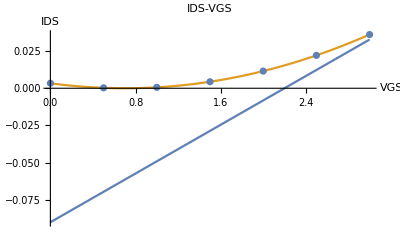

```mathematica
NMOSCurrentSeperateRegion=Plot[{NIDT[VG,3,0,50,.50,0],NIDS[VG,3,0,50,.50,0]},{VG,0,3}];
(*Table[{VG,NIds[VG,3,0,50,0.5,0]},{VG,0,5,0.5}]*)
NMOSCurrentOneRegion=ListPlot[Table[{VG,NIds[VG,3,0,50,0.5,0]},{VG,0,3,0.5}]];
Show[NMOSCurrentSeperateRegion,NMOSCurrentOneRegion,PlotLabel->"IDS-VGS",AxesLabel->{VGS,IDS}]
```

PMOS

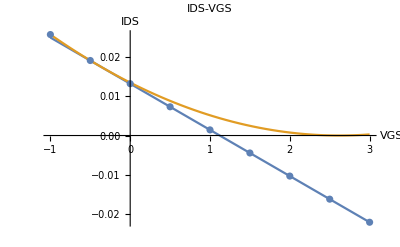

```mathematica
PMOSCurrentSeperateRegion=Plot[{PIDT[VG,0,3,50,.50,0],PIDS[VG,0,3,50,.50,0]},{VG,-1,3}];
PMOSCurrentOneRegion=ListPlot[Table[{VG,PIds[VG,0,3,50,0.5,0]},{VG,3,-1,-0.5}]];
Show[PMOSCurrentSeperateRegion,PMOSCurrentOneRegion,PlotLabel->"IDS-VGS",AxesLabel->{VGS,IDS}]
```

#### question 2.2

```mathematica
Ngm=Sqrt[2 NUO COX W/L 0.5 10^-3(1+NLAMBDA 3)]/.W->50/.L->.5;
Ngm/(NLAMBDA 0.5 10^-3)
Pgm=Sqrt[2 PUO COX W/L 0.5 10^-3(1+PLAMBDA 3)]/.W->50/.L->.5;
Pgm/(PLAMBDA 0.5 10^-3)
```

84.2496

24.98

#### question 2.3

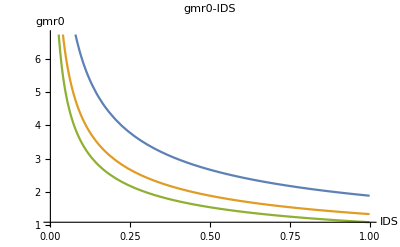

```mathematica
NgmNr0[VDS_,IDT_,W_,L_]:=(1/(L NLAMBDA)) Sqrt[2 NUO COX W] Sqrt[1/IDT]Sqrt[L+L NLAMBDA VDS]
Plot[{NgmNr0[3,IDT,50,0.5],NgmNr0[3,IDT,50,1],NgmNr0[3,IDT,50,1.5]},{IDT,0,1},PlotLabel->"gmr0-IDS",AxesLabel->{IDS,gmr0}]
```

#### question 2.4

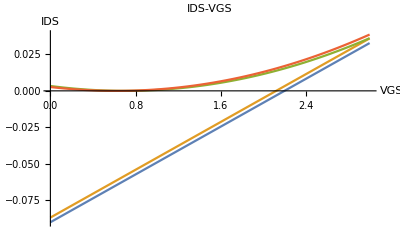

```mathematica
Plot[{NIDT[VG,3,0,50,.50,0],NIDT[VG,3,0,50,.50,1.5],NIDS[VG,3,0,50,.50,0],NIDS[VG,3,0,50,.50,1.5]},{VG,0,3},PlotLabel->"IDS-VGS",AxesLabel->{VGS,IDS}]
```

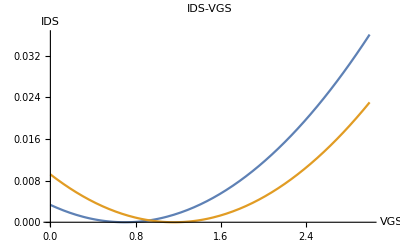

```mathematica
Plot[{NIDS[VG,3,0,50,.50,0],NIDS[VG,3,0,50,.50,-3]},{VG,0,3},PlotLabel->"IDS-VGS",AxesLabel->{VGS,IDS}]
```

#### question 2.5

(a)

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

1.9652

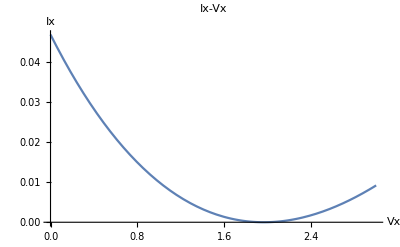

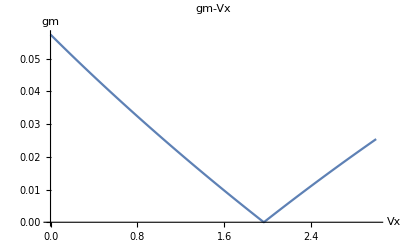

```mathematica
FindRoot[NIds[3,3,x,50,0.5,0]==0,{x,1.5}][[1,2]]//N
Plot[NIds[3,3,VX,50,0.5,0] (1+NLAMBDA (3-VX)),{VX,0,3},PlotLabel->"Ix-Vx",AxesLabel->{Vx,Ix}]
Plot[Sqrt[2 NUO NIds[3,3,VX,50,0.5,0] (1+NLAMBDA (3-VX))],{VX,0,3},PlotLabel->"gm-Vx",AxesLabel->{Vx,gm}]
```

(b)

1.20621

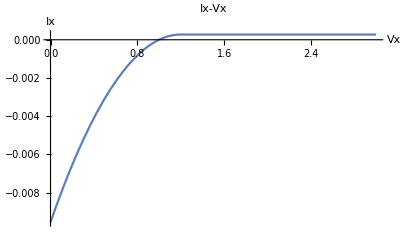

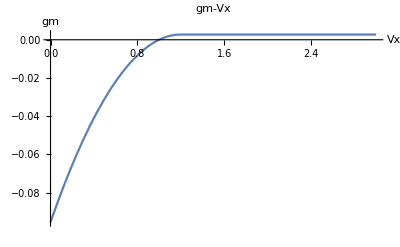

```mathematica
FindRoot[D[NIds[1.9,VX,1,50,0.5,1],VX]==0,{VX,1}][[1,2]]
Plot[NIds[VG,VX,VS,50,0.5,VB]/.{VG->1.9,VS->1,VB->1}(* (1+NLAMBDA (VX-1))*),{VX,0,3}(*,PlotRange->{{-10^-6,10^-6}}*),PlotLabel->"Ix-Vx",AxesLabel->{Vx,Ix}]
Plot[2 NIds[VG,VX,VS,50,0.5,VB]/NVEFF/.NVEFF->VG-VS-NVTH/.NVTH->NVTO+NGAMMA (Sqrt[Abs[NPHI+VS-VB]]-Sqrt[NPHI])/.VG->1.9/.VS->1/.VB->1,{VX,0,3},PlotLabel->"gm-Vx",AxesLabel->{Vx,gm}]
```

```mathematica
(*μ=350 10^-4;cox=3.9 10^-3;w=10^-6;l=10^-6;vth=0.7;*)
ids[vgs_,vds_]:=μ cox w/l ((vgs-vth) vds-0.5 vds^2)/;vgs<vth
ids[vgs_,vds_]:=0.5 μ cox w/l (vgs-vth)^2/;vgs≥vth
```

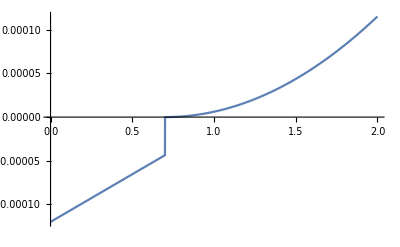

```mathematica
Plot[ids[vgs,0.8],{vgs,0,2}]
```

```mathematica
Clear[vdd,rd,μ,cox,w,l,vth];
(*vdd=5;rd=1000;*)
vout[vin_]:=vdd-rd 0.5 μ cox w/l (vin-vth)^2/;vin>vth
vout'[vin]
vout'[vin]/.μ cox w/l (vin-vth)->gm
```

-(1. cox rd (vin-vth) w μ)/l

-1. gm rd

```mathematica
Clear["Global`*"]
dd={vdd->5,rd->1000,μ->350 10^-4,cox->3.9 10^-3,w->10^-6,l->10^-6,vth->0.7};
vout[vin_,vds_]:=vdd-rd 0.5 μ cox w/l (2(vin-vth) vds-vds^2)
D[vout[vin,vds],vin]
vv[vin_,vds_]:=vout[vin,vds]/rd//Simplify
vv[vin,vds];D[vv[vin,vds],vin];vv[vin,vds]/.dd;Plot[vv[vin,0.8]/.dd,{vin,0.7,5}]
```

-(1. cox rd vds w μ)/l

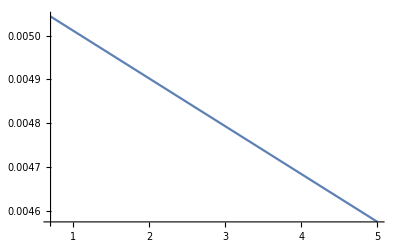

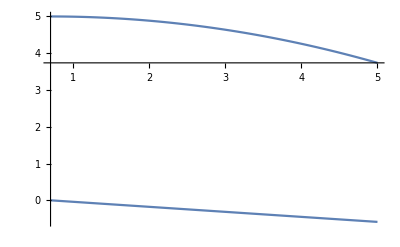

```mathematica
dd={vdd->5,rd->1000,μ->350 10^-4,cox->3.9 10^-3,w->10^-6,l->10^-6,vth->0.7};
Show[{Plot[vout[vin]/.dd,{vin,0.7,5}],Plot[vout'[vin]/.dd,{vin,0.7,5}]},PlotRange->All]
```

```mathematica
Clear[vout]
vout[vin_]:=vdd-rd 0.5 μ cox w/l (2(vin-vth) vds-vds^2)
vout'[vin]
```

-(1. cox rd vds w μ)/l

```mathematica
Solve[D[vvout==vdd-rd 0.5 μ cox w/l (2(vin-vth) vvout-vvout^2),vvout],vvout]//Simplify
```

{{vvout→1. vin-1. vth+(1. l)/(cox rd w μ)}}

```mathematica
Solve[vvout==vdd-rd 0.5 μ cox w/l (2(vin-vth) vvout-vvout^2),vvout]//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vvout→(l+cox rd vin w μ-1. cox rd vth w μ-1. l √((-2. cox l rd vdd w μ+(1. l+cox rd (vin-1. vth) w μ)^2)/l^2))/(cox rd w μ)},{vvout→(l+cox rd vin w μ-1. cox rd vth w μ+l √((-2. cox l rd vdd w μ+(1. l+cox rd (vin-1. vth) w μ)^2)/l^2))/(cox rd w μ)}}